```mathematica
SetDirectory["/Users/mobileryan/Triplet-ESR"]
```

/Users/mobileryan/Triplet-ESR

```mathematica
SetDirectory["C:\\Users\\goluc\\Desktop\\nonLinearFit"]
```

C:\Users\goluc\Desktop\nonLinearFit

```mathematica
preData=Import["./test.dat","CSV" ];
{dimT, dump}=Dimensions[preData[[2;;-1]]]
BData=Drop[Drop[preData[[1]],1],-1];
dimB=Length[BData]
DataB[B_]:=Table[{preData[[i,1]],preData[[i,B+1]]},{i,2,dimT}]
DataT[t_]:=Table[{preData[[1,i]],preData[[t+1,i+1]]},{i,1,dimB}]
```

{1002,352}

350

```mathematica
tempData=preData[[2;;-1, 2;;-1]];
ArrayPlot[tempData,ColorFunction->"Rainbow",AspectRatio->1]
{Max[tempData], Min[tempData]}
```

-Graphics-

{Max[41.34,],Min[-34.17,]}

```mathematica
Manipulate[
Module[{dataT},
dataT=DataT[startT];
ListPlot[dataT,Joined->True, AspectRatio->1/10,PlotRange->All, ImageSize->Full, PlotLabel->ToString[startT]<>", Time = "<>ToString[preData[[startT+1,1]]]<>", Max = "<> ToString[Max[dataT[[1;;-1,2]]]]<>", Min = "<>ToString[ Min[dataT[[1;;-1,2]]]]] 
],
{{startT,207},1,dimT,1}]
```

```mathematica
Manipulate[
Module[{dataB},
dataB=DataB[startB];
ListPlot[dataB,Joined->True, AspectRatio->1/10,PlotRange->All, ImageSize->Full, PlotLabel->ToString[startB]<>", B-field = "<>ToString[preData[[1,startB]]]<>", Max = "<> ToString[Max[dataB[[1;;-1,2]]]]<>", Min = "<>ToString[ Min[dataB[[1;;-1,2]]]]]
] ,
{{startB,105},1,dimB,1}]
```

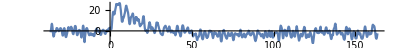

{B-Field,3.217,2.4,mean,-0.591314,sd,2.88235}

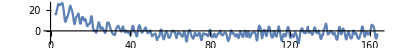

```mathematica
startB=105;
dataB=DataB[startB];
fitStartT=195;
ListPlot[dataB, Joined->True, AspectRatio->1/10,PlotRange->All, ImageSize->Full] 
{"B-Field",BData[[startB]],dataB[[fitStartT,1]],"mean",noiseLevel=Mean[dataB[[1;;fitStartT-20,2]]], "sd",sd=StandardDeviation[dataB[[1;;fitStartT-20,2]]]}
g1=ListPlot[dataB[[fitStartT;;-1]], Joined->True, AspectRatio->1/10,PlotRange->All, ImageSize->Full]
```

```mathematica
Func[t_,a_,Ta_]:=a Exp[-t/Ta]
f[t_,par_]:=Func[t,par[[1]],par[[2]]]+Func[t,par[[3]],par[[4]]]
F[t_,par_]:={ⅇ^(-t/par[[2]]),(par[[1]] ⅇ^(-t/par[[2]]) t)/par[[2]]^2,ⅇ^(-t/par[[4]]),(par[[3]] ⅇ^(-t/par[[4]]) t)/par[[4]]^2}
```

```mathematica
nlm=NonlinearModelFit[dataB[[fitStartT;;-1]],{f[t,{a,Ta,b,Tb}+c], a>0, b<0, 0<Ta <Tb}, {a, Ta, b, Tb,c}, t,AccuracyGoal->1, PrecisionGoal->1];
nlm[{"ParameterTable","ANOVATable"}]
```

{ | Estimate | Standard Error | t-Statistic | P-Value
a | 41.5584 | 9.04793 | 4.59314 | 5.06839×10^-6
Ta | 22.3432 | 6.04464 | 3.69636 | 0.000233587
b | -14.7958 | 3.0768 | -4.80882 | 1.81319×10^-6
Tb | 73.5229 | 15.4306 | 4.76474 | 2.24454×10^-6
c | 0.722791 | 3.33224 | 0.216908 | 0.828335, | DF | SS | MS
Model | 5 | 26676.7 | 5335.34
Error | 802 | 9068.58 | 11.3075
Uncorrected Total | 807 | 35745.3 | 
Corrected Total | 806 | 35736.8 | }

{ | Estimate | Standard Error | t-Statistic | P-Value
a | 42.2812 | 5.75785 | 7.34323 | 5.12256×10^-13
Ta | 23.066 | 2.84311 | 8.11294 | 1.84675×10^-15
b | -14.073 | 6.27388 | -2.24311 | 0.025162
Tb | 74.2457 | 18.7473 | 3.96035 | 0.000081486, | DF | SS | MS
Model | 4 | 26676.7 | 6669.18
Error | 803 | 9068.58 | 11.2934
Uncorrected Total | 807 | 35745.3 | 
Corrected Total | 806 | 35736.8 | , | Estimate | Standard Error | Confidence Interval
a | 42.2812 | 5.75785 | {30.979,53.5834}
Ta | 23.066 | 2.84311 | {17.4852,28.6468}
b | -14.073 | 6.27388 | {-26.3881,-1.75783}
Tb | 74.2457 | 18.7473 | {37.4463,111.045}}

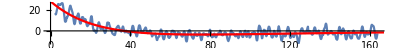

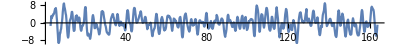

{mean,0.035846,sd,3.32279,1.15281}

```mathematica
nlm=NonlinearModelFit[dataB[[fitStartT;;-1]],{f[t,{a,Ta,b,Tb}], a>0, b<0, 0<Ta <Tb}, {a, Ta, b, Tb}, t,AccuracyGoal->1, PrecisionGoal->1];
nlm[{"ParameterTable","ANOVATable","ParameterConfidenceIntervalTable"}]
Show[
g1,
Plot[nlm[t],{t,0,200}, PlotRange->All, PlotStyle->Red]
]
diff=Table[{dataB[[i,1]],dataB[[i,2]]-nlm[dataB[[i,1]]]},{i,200,Length[dataB]}];
ListPlot[diff, Joined->True, AspectRatio->1/10,PlotRange->All, ImageSize->Full]
{"mean",Mean[diff[[1;;-1,2]]], "sd",fitSigma=StandardDeviation[diff[[1;;-1,2]]], fitSigma/sd}
```

```mathematica
FindFit[dataB[[fitStartT;;-1]],a Exp[-t/Ta]+b Exp[-t/Tb],{{a,20},{Ta,20},{b,-10},{Tb,80}},t,WorkingPrecision->10]
```

{a→40.07998471,Ta→19.39630731,b→-9.104777047,Tb→96.86984992}

## Manual Method

```mathematica
X=dataB[[fitStartT;;-1]][[1;;-1,1]];
Y=dataB[[fitStartT;;-1]][[1;;-1,2]];
n=Length[X];
SSRcoun= Table[{b, Tb, 
fn =Table[f[X[[i]], {55, 28, b, Tb}],{i,Length[X]}];
SSRn=(Y - fn).(Y-fn)/n},{b,-40,-20, 2}, {Tb, 20, 80,2}];
{mi,mj}=Dimensions[SSRcoun][[{1,2}]];
Min[Table[SSRcoun[[i,j,3]],{i,1,mi},{j,1,mj}]]
%*n
```

8.80606

7106.49

```mathematica
12 n
```

9684

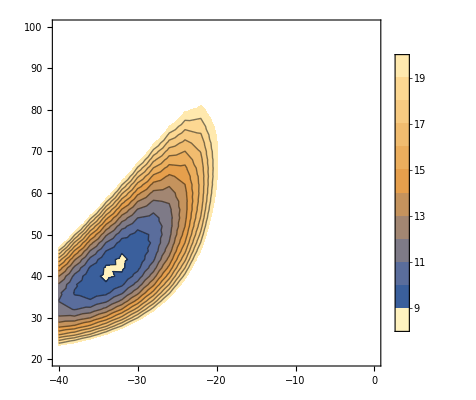

```mathematica
ListContourPlot[Flatten[SSRcoun,1],
PlotRange->{0,20},
Contours->Table[i,{i,7,20,1}],
InterpolationOrder->3,PlotLegends->Automatic]
```

```mathematica
DF=803;α=0.95;
tStat=Table[temp[[1,i]]/temp[[2,i]],{i,1,4}]
pValue=Table[2(1-CDF[StudentTDistribution[DF],Abs[tStat[[i]]]]),{i,1,4}]
CF=Table[
temp[[1,i]]+
temp[[2,i]]{InverseCDF[StudentTDistribution[DF],(1-α)/2],InverseCDF[StudentTDistribution[DF],(1+α)/2]},{i,1,4}]
```

{1.74526,4.84665,-0.678331,2.36191}

{0.0813214,1.50736×10^-6,0.497757,0.018419}

{{-8.03612,136.909},{17.9915,42.4848},{-98.8684,48.0853},{9.37862,101.661}}

```mathematica
newPar2[par_,dataB_]:=Module[
{fa,Fa, Y,X, par1,CoVar, error, var, DF, GMat},
X=dataB[[1;;-1,1]];
Y=dataB[[1;;-1,2]];
fa=Table[Func[X[[i]], par[[1]],par[[2]]],{i,Length[X]}];
Fa=Table[F2[X[[i]], par],{i,Length[X]}];
GMat=Inverse[Transpose[Fa].Fa].Transpose[Fa];
par1=par+GMat.(Y-fa);
DF=Length[X]-Length[par];
var=(Y-fa).(Y-fa)/DF;
CoVar=var Inverse[Transpose[Fa].Fa];
error=Table[√CoVar[[i,i]],{i,1,Length[par]}];
{par1,error, var,DF}
]
```

```mathematica
temp2=newPar2[{50,30},dataB[[fitStartT;;-1]]]
temp2=newPar2[temp2[[1]],dataB[[fitStartT;;-1]]]
temp2=newPar2[temp2[[1]],dataB[[fitStartT;;-1]]]
temp2=newPar2[temp2[[1]],dataB[[fitStartT;;-1]]]
temp2=newPar2[temp2[[1]],dataB[[fitStartT;;-1]]]
temp2=newPar2[temp2[[1]],dataB[[fitStartT;;-1]]]
temp2=newPar2[temp2[[1]],dataB[[fitStartT;;-1]]]
temp2=newPar2[temp2[[1]],dataB[[fitStartT;;-1]]]
```

{{42.0385,18.115},{1.32321,1.03401},47.0199,805}

{{43.21,18.0827},{0.909289,0.483381},10.8097,805}

{{43.1979,18.0916},{0.908267,0.468798},10.7557,805}

{{43.2012,18.0894},{0.907925,0.469012},10.7557,805}

{{43.2004,18.0899},{0.908009,0.468955},10.7557,805}

{{43.2006,18.0898},{0.907988,0.468969},10.7557,805}

{{43.2005,18.0898},{0.907994,0.468966},10.7557,805}

{{43.2005,18.0898},{0.907992,0.468966},10.7557,805}

```mathematica
nlm2[{"ParameterTable","ANOVATable","ParameterConfidenceIntervalTable"}]
```

{ | Estimate | Standard Error | t-Statistic | P-Value
a | 43.2005 | 0.907993 | 47.5781 | 3.98102×10^-236
Ta | 18.0898 | 0.468966 | 38.5738 | 3.69199×10^-185, | DF | SS | MS
Model | 2 | 64018.5 | 32009.3
Error | 805 | 8658.36 | 10.7557
Uncorrected Total | 807 | 72676.9 | 
Corrected Total | 806 | 64550.3 | , | Estimate | Standard Error | Confidence Interval
a | 43.2005 | 0.907993 | {41.4182,44.9828}
Ta | 18.0898 | 0.468966 | {17.1693,19.0104}}

```mathematica
DF2=805;α=0.95;
tStat2=Table[temp2[[1,i]]/temp2[[2,i]],{i,1,2}]
pValue2=Table[2(1-CDF[StudentTDistribution[DF2],Abs[tStat2[[i]]]]),{i,1,2}]
CF2=Table[
temp2[[1,i]]+
temp2[[2,i]]{InverseCDF[StudentTDistribution[DF2],(1-α)/2],InverseCDF[StudentTDistribution[DF2],(1+α)/2]},{i,1,2}]
```

{47.5777,38.5742}

{0.,0.}

{{41.4182,44.9828},{17.1693,19.0104}}

## Fourier Analysis

```mathematica
SwapData[fdata_]:=Module[{n},
n=Length[fdata];
Join[fdata[[2+(n-1)/2;;-1]],fdata[[1;;1+(n-1)/2]]]
]
SwapDataBack[fdata_]:=Module[{n},
n=Length[fdata];
Join[fdata[[1+(n-1)/2;;-1]],fdata[[1;;(n-1)/2]]]
]
```

807

0.2

0.00619579

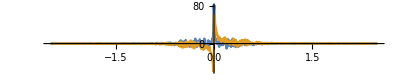

```mathematica
data=dataB[[fitStartT;;-1]];
(*data=Table[{t,Exp[-2π t]},{t,0,3,ΔT}];*)
n=Length[data]
(* n must be odd  for the moment*)
ΔT = data[[2,1]]-data[[1,1]]
ω=1/(n ΔT) 
ftestYp=Fourier[data[[1;;-1,2]], FourierParameters->{0,1}];
ftestY=SwapData[ftestYp];
ftestRe=Table[{ω (i-1-(n-1)/2),Re[ftestY[[i]]]},{i,1,n}];
ftestIm=Table[{ω (i-1-(n-1)/2),Im[ftestY[[i]]] },{i,1,n}];
ListPlot[{ftestRe,ftestIm},Joined->True,PlotRange->All,ImageSize->Full,AspectRatio->1/5]
```

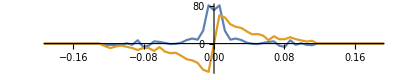

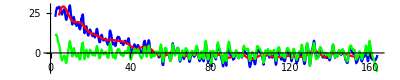

```mathematica
gate = 20;
fRange ={10,-40};
ftestYS=Table[If[Abs[i-(n-1)/2]<gate,ftestY[[i]],0],{i,1,n}];
ftestYSN=Table[If[Abs[i-(n-1)/2]≥ gate,ftestY[[i]],0],{i,1,n}];
fftestYN=InverseFourier[SwapDataBack[ftestYSN]]//Chop;
fftestN=Table[{data[[i,1]],Re[fftestYN[[i]]]},{i,1,n}];
ftestSRe=Table[{ω (i-1-(n-1)/2),Re[ftestYS[[i]]]},{i,1,n}];
ftestSIm=Table[{ω (i-1-(n-1)/2),Im[ftestYS[[i]]]},{i,1,n}];
ListPlot[{ftestSRe,ftestSIm},Joined->True, ImageSize->Full,AspectRatio->1/5, PlotRange->{{-ω gate 1.5,ω gate 1.5},All}]
fftestY=InverseFourier[SwapDataBack[ftestYS]]//Chop;
fftest=Table[{data[[i,1]],Re[fftestY[[i]]]},{i,1,n}];
ListPlot[{data,fftest[[fRange[[1]];;fRange[[2]]]],fftestN},Joined->True,PlotRange->All,ImageSize->Full,AspectRatio->1/5, PlotStyle->{Blue, Red, Green}]
```

{{ | Estimate | Standard Error | t-Statistic | P-Value
a | 2507.58 | 4.45905×10^6 | 0.000562358 | 0.999551
Ta | 38.9619 | 319.615 | 0.121903 | 0.903009
b | -2473.07 | 4.45905×10^6 | -0.000554619 | 0.999558
Tb | 39.3224 | 325.907 | 0.120655 | 0.903996},{ | Estimate | Standard Error | t-Statistic | P-Value
a | 5047.87 | 8.73341×10^7 | 0.0000577995 | 0.999954
Ta | 41.7298 | 1636.66 | 0.0254969 | 0.979665
b | -5015.2 | 8.73341×10^7 | -0.0000574254 | 0.999954
Tb | 41.9192 | 1652.29 | 0.0253703 | 0.979766}}

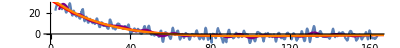

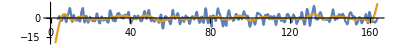

```mathematica
nlm2=NonlinearModelFit[fftest[[fRange[[1]];;fRange[[2]]]],{f[t,{a,Ta,b,Tb}], a>0, b<0, 0<Ta <Tb}, {a, Ta, b, Tb}, t,AccuracyGoal->1, PrecisionGoal->1];
{nlm2[{"ParameterTable"}],nlm[{"ParameterTable"}]}
Show[
g1,
ListPlot[fftest[[fRange[[1]];;fRange[[2]]]],Joined->True,PlotRange->All,PlotStyle->Purple],
Plot[{nlm[t],nlm2[t]},{t,0,200}, PlotRange->All, PlotStyle->{Red, Orange}]
]
diff2=Table[{fftest[[i,1]],fftest[[i,2]]-nlm2[fftest[[i,1]]]},{i,1,Length[fftest]}];
ListPlot[{diff,diff2}, Joined->True, AspectRatio->1/10,PlotRange->All, ImageSize->Full]
```